```mathematica
pKlBlei= {{0.41,5.285},{0.22,5.859},{0.11,6.456},{0.058,6.978},{0.03,7.422},{0.015,7.839}};
interpolatepKlBlei = Interpolation[pKlBlei];
interpolateValue = interpolatepKlBlei[0]
```

8.43731

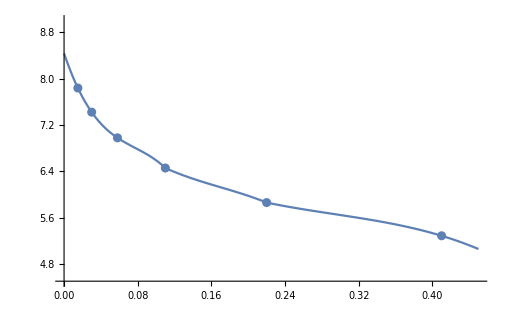

```mathematica
modellpKlBlei = Plot[interpolatepKlBlei[x],{x,0,0.45},PlotRange->{4.5,9}];
graphpKlBlei = ListPlot[pKlBlei];
Show[modellpKlBlei,graphpKlBlei]
```